```mathematica
diagramd=Import["G:\\calc-online\\gpd\\pic\\1-pic3Dlist-e-n.wdx"];
ef1=Query[1,1]@diagramd;
eg1=Query[1,2]@diagramd;
```

```mathematica
syef=Interpolation[Flatten[ef1,1]];
syeg=Interpolation[Flatten[eg1,1]];
```

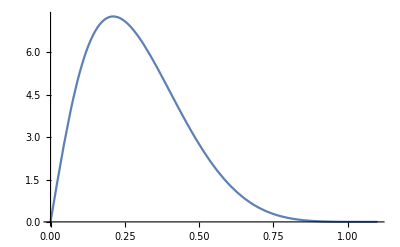

```mathematica
Plot[I*syef[x,-1],{x,0,1.1}]
```

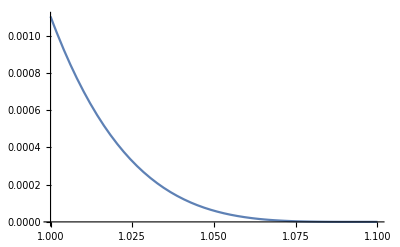

```mathematica
Plot[I*syef[x,-1],{x,1,1.1}]
```